```mathematica
Needs["PlotLegends`"]
```

## General

### Run This to browse

```mathematica
Manipulate[plotROC[funcname, xnoise, ynoise, nsamp, nbin],{funcname,Union[functionName/@rocFileNames]}, {xnoise,Union[xNoise/@rocFileNames]}, {ynoise,Union[yNoise/@rocFileNames]}, {nsamp,Union[nSamples/@rocFileNames]}, {nbin,Union[nBins/@rocFileNames]}]
```

## Code

### Data file list

This is the global variable for the filenames containing the roc data. The filenames encode metadata about the contained data.

```mathematica
rocFileNames=FileNames["*.roc.tsv",{"../rocs"}];
```

#### Testing

```mathematica
rocFileNames[[1]]
```

../rocs/00001_parabolic_x000_y000.s005.b001.roc.tsv

```mathematica
rocFileNames[[140]]
```

../rocs/00001_parabolic_x000_y010.s006.b001.roc.tsv

```mathematica
rocFileNames[[440]]
```

../rocs/00001_parabolic_x010_y000.s010.b010.roc.tsv

```mathematica
StringSplit[rocFileNames[[1]],"_"]
```

{../rocs/00001,parabolic,x000,y000.s005.b001.roc.tsv}

### File name metadata extraction

The functions in this section are for extracting metadata from the function names

##### Function name

```mathematica
functionName[filename_String]:=With[{parts=StringSplit[filename,"_"]},
With[{lastPart=Length[parts]-2},
If[lastPart>2,
StringJoin[Flatten[{parts[[2]],{"_",#}&/@parts[[Range[3,lastPart]]]}]],
parts[[2]]]
]]
```

##### Testing

```mathematica
Range[2,10]
```

{2,3,4,5,6,7,8,9,10}

```mathematica
{1,a,3,c,5}[[{2,3,4}]]
```

{a,3,c}

```mathematica
functionName["00351_L_x000_y000.s005.b001.roc.tsv"]
```

L

```mathematica
functionName["00351_L_lop_x000_y000.s005.b001.roc.tsv"]
```

L_lop

```mathematica
functionName["00351_Gold_L_lop_x000_y000.s005.b001.roc.tsv"]
```

Gold_L_lop

##### X-axis noise level

```mathematica
xNoise[filename_String]:=With[{split=StringSplit[filename,"_"]},ToExpression[StringDrop[split[[Length[split]-1]],1]]/100
]
```

##### Testing

```mathematica
xNoise[rocFileNames[[1]]]
```

0

```mathematica
xNoise[rocFileNames[[440]]]
```

1/10

```mathematica
xNoise["00351_L_lop_x000_y000.s005.b001.roc.tsv"]
```

0

```mathematica
xNoise["00351_L_lop_x010_y000.s005.b001.roc.tsv"]
```

1/10

##### Y-axis noise level

```mathematica
yNoise[filename_String]:=With[{split=StringSplit[filename,"_"]},ToExpression[StringDrop[StringSplit[Last[split],"."][[1]],1]]/100]
```

##### Testing

```mathematica
yNoise[rocFileNames[[440]]]
```

0

```mathematica
yNoise[rocFileNames[[140]]]
```

1/10

```mathematica
yNoise["00351_L_lop_x000_y030.s005.b001.roc.tsv"]
```

3/10

```mathematica
yNoise["00351_L_lop_x010_y000.s005.b001.roc.tsv"]
```

0

##### Number of samples

```mathematica
nSamples[filename_String]:=With[{split=StringSplit[filename,"_"]},ToExpression[StringDrop[StringSplit[Last[split],"."][[2]],1]]
]
```

##### Testing

```mathematica
nSamples[rocFileNames[[440]]]
```

10

```mathematica
nSamples[rocFileNames[[140]]]
```

6

##### Number of bins

```mathematica
nBins[filename_String]:=
With[{split=StringSplit[filename,"_"]},ToExpression[StringDrop[StringSplit[Last[split],"."][[3]],1]]
]
```

##### Testing

```mathematica
nBins[rocFileNames[[440]]]
```

10

```mathematica
nBins[rocFileNames[[140]]]
```

1

### Plot a single ROC curve

```mathematica
plotROC[funcname_, xnoise_, ynoise_, nsamp_, nbin_]:=With[{filenames=Select[rocFileNames,functionName[#]==funcname&&xNoise[#]==xnoise&&yNoise[#]==ynoise&&nSamples[#]==nsamp&&nBins[#]==nbin&]},If[Length[filenames]==0,"The requested ROC curve has not been calculated",
With[{data=Import[filenames[[1]]]},ListLinePlot[data,PlotRange->All]
]]]
```

#### Testing

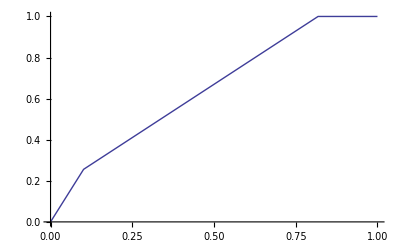

```mathematica
plotROC["parabolic",0,0,6,4]
```

### Plot all mic scores for a given function, noise condition, and number of samples

```mathematica
plotMicROCs[funcname_, xnoise_, ynoise_, nsamp_]:=With[{filenames=Sort[Select[rocFileNames,functionName[#]==funcname&&xNoise[#]==xnoise&&yNoise[#]==ynoise&&nSamples[#]==nsamp&&nBins[#]≥4&],nBins[#1]<nBins[#2]&]},If[Length[filenames]==0,"The requested ROC curves have not been calculated",
With[{data=MapIndexed[Tooltip[#1,nBins[filenames[[#2]][[1]]]]&,Import/@filenames]},
With[{dashStyles={Dashing[{}],Dashed,Dotted,DotDashed},colors=If[Length[data]>1,Table[ColorData["DarkRainbow"][x],{x,0,1,1/(Length[data]-1)}],{Blue}]},
With[{styles=MapIndexed[Directive[#1,dashStyles[[Mod[#2[[1]],Length[dashStyles]]+1]] ]&,colors]},
If[Length[data]>10,
ListLinePlot[data,PlotRange->All,PlotStyle->styles,ImageSize->{1024}],
ListLinePlot[data,PlotRange->All,PlotStyle->styles,ImageSize->{1024},PlotLegend->nBins/@filenames,LegendPosition->{0.8,-0.3}]
]
]]]]]
```

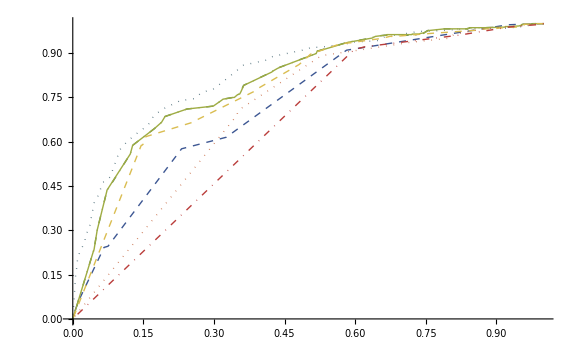

```mathematica
plotMicROCs["parabolic",1/10,1/10,14]
```

```mathematica
Export["foo.svg",plotMicROCs["parabolic",1/10,1/10,12]]
```

foo.svg

```mathematica
Export["foo.png",plotMicROCs["parabolic",1/10,1/10,12]]
```

foo.png

### Zero pad

Return number padded on the right with 0's to have places digits

```mathematica
zeroPad[num_,places_]:=ToString[PaddedForm[num,places,NumberPadding->{"0",""},NumberSigns->{"",""}]]
```

### Export plot to appropriately named png

```mathematica
exportPlotMicROCs[funcname_, xnoise_, ynoise_, nsamp_]:=With[{destname=funcname<>".x."<>zeroPad[xnoise 100,3]<>".y."<>zeroPad[ynoise 100,3]<>".s."<>zeroPad[nsamp,3]<>".png"},Export[destname,plotMicROCs[funcname,xnoise,ynoise,nsamp]]
]
```

```mathematica
exportPlotMicROCs["parabolic",1/10,1/10,12]
```

parabolic.x.010.y.010.s.012.png

### List of all the plot parameters to export

```mathematica
micROCsToExport[]:=With[{
funcs=Union[functionName/@rocFileNames],xnoises=Union[xNoise/@rocFileNames],
ynoises=Union[yNoise/@rocFileNames],
samps=Union[nSamples/@rocFileNames]},
Tuples[{funcs,xnoises,ynoises,samps}]
]
```

```mathematica
Apply[exportPlotMicROCs,#]&/@Take[micROCsToExport[],5]
```

{23halton.x.000.y.000.s.005.svg,23halton.x.000.y.000.s.006.svg,23halton.x.000.y.000.s.007.svg,23halton.x.000.y.000.s.008.svg,23halton.x.000.y.000.s.009.svg}

{{23halton,0,0,5},{23halton,0,0,6},{23halton,0,0,7},{23halton,0,0,8},{23halton,0,0,9}}

```mathematica
Length[Select[micROCsToExport[],#[[4]]<30&]]
```

4212

```mathematica
ParallelMap[Apply[exportPlotMicROCs,#]&,Select[micROCsToExport[],#[[4]]<30&]]
```

### Calculate AUC for the ROC curve in a file

Return the area below a horizontal line from the point with the lower x coordinate to the point directly below or above the other point

```mathematica
horizArea[p1_List,p2_List]:=If[p2[[1]]<p1[[1]],horizArea[p2,p1],
(p2[[1]]-p1[[1]])p1[[2]]]
```

Calculate the area under an ROC curve given by the points in data. Points are added to ensure that all lines are horizontal. This is accurate in the case of the MIC due to the discrete nature of the points. For the non-mic scores, there are enough points that the approximation is not too far off.

```mathematica
auc[data_List]:=With[{d=Sort[data,#1[[1]]<#2[[1]]&]},
With[{areas=Map[horizArea[d[[#]],d[[#+1]]]&,Range[Length[d]-1]]},
Total[areas]
]]
```

```mathematica
auc[{{5,10},{1,1},{3,5}}]
```

12

Calculate the AUC of the data stored in the given file

```mathematica
auc[filename_String]:=auc[Import[filename]]
```

```mathematica
Union[(nBins[#1] & ) /@ rocFileNames]
```

{1,2,3,4,6,8,9,10,12,14,15,16,18,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100}

```mathematica
allAUCs=ParallelMap[{functionName[#],xNoise[#],yNoise[#],nSamples[#],nBins[#],auc[#]}&,rocFileNames];
```

$Aborted

```mathematica
allAUCs[[138]]
```

{parabolic,0,1/10,5,3,auc[../rocs/00001_parabolic_x000_y010.s005.b003.roc.tsv]}

## L-shaped

```mathematica
l10106020=Import["../rocs/00350_L_x010_y010.s060.b020.roc.tsv"];
```

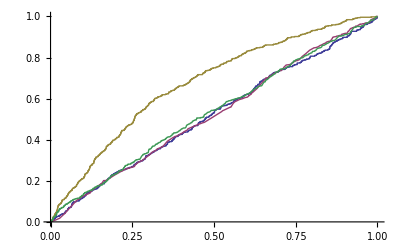

```mathematica
ListLinePlot[{l10106020,l10103018,l10103001,l10103002},PlotLegend->{20,18,"DCor","Spear"},LegendPosition->{0.5,-0.45}]
```

```mathematica
l10103018=Import["../rocs/00350_L_x010_y010.s030.b018.roc.tsv"];
```

```mathematica
l10103001=Import["../rocs/00350_L_x010_y010.s030.b001.roc.tsv"];
```

```mathematica
l10103002=Import["../rocs/00350_L_x010_y010.s030.b002.roc.tsv"];
```

## Parabola w 0.1 0.1 noise

```mathematica
p10106020=Import["../rocs/00001_parabolic_x010_y010.s060.b020.roc.tsv"];
```

```mathematica
p10103018=Import["../rocs/00001_parabolic_x010_y010.s030.b018.roc.tsv"];
```

```mathematica
p10103001=Import["../rocs/00001_parabolic_x010_y010.s030.b001.roc.tsv"];
```

```mathematica
p10103002=Import["../rocs/00001_parabolic_x010_y010.s030.b002.roc.tsv"];
```

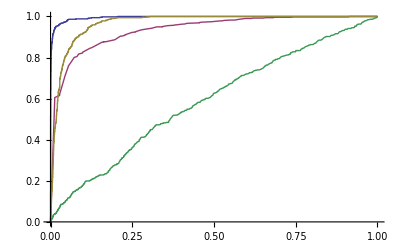

```mathematica
ListLinePlot[{p10106020,p10103018,p10103001,p10103002},PlotRange->All, PlotLegend->{20,18,"DCor","Spear"},LegendPosition->{0.5,-0.45}]
```

## Dependence Method AUC difference distributions

I want to look at the distributions of the differences in the AUC score for different methods. Note that I am looking at only the non-pathological relations.

```mathematica
rankedAUCData=Import["../ranked_aucs_nonpath.tsv"];
```

```mathematica
InputForm[rankedAUCData[[1]]]
```

{"rocs/00001_parabolic_x000_y000.s005", ".b001.roc.tsv", 0.73243713378906, 
 ".b002.roc.tsv", 0.551128387427734, ".b003.roc.tsv", 0.622145758730474, 
 ".b004.roc.tsv", 0.634223302108399, 0, 0.181308746361326, 0.110291375058586, 
 0.098213831680661, -0.181308746361326, 0, -0.07101737130274, -0.083094914680665, 
 -0.110291375058586, 0.07101737130274, 0, -0.012077543377925, -0.098213831680661, 
 0.083094914680665, 0.012077543377925, 0, ".b002.roc.tsv", 0.551128387427734, 
 ".b003.roc.tsv", 0.622145758730474, ".b004.roc.tsv", 0.634223302108399, 
 ".b001.roc.tsv", 0.73243713378906}

```mathematica
Length[rankedAUCData[[1]]]
```

33

```mathematica
Take[rankedAUCData[[1]],-8]
```

{.b002.roc.tsv,0.551128,.b003.roc.tsv,0.622146,.b004.roc.tsv,0.634223,.b001.roc.tsv,0.732437}

```mathematica
Take[rankedAUCData[[1]],-8][[Range[4] 2-1]]
```

{.b002.roc.tsv,.b003.roc.tsv,.b004.roc.tsv,.b001.roc.tsv}

```mathematica
Take[rankedAUCData[[1]],-8][[Range[4] 2]]
```

{0.551128,0.622146,0.634223,0.732437}

### MIC

When is (and by how much) is dcor better than MIC

```mathematica
dcorMinusBestMIC=#[[13]]&/@rankedAUCData;
```

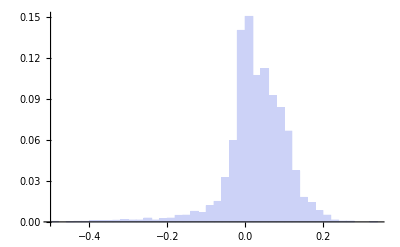

```mathematica
Histogram[dcorMinusBestMIC,Automatic,"Probability"]
```

```mathematica
Mean[dcorMinusBestMIC]
```

0.0296047

```mathematica
Median[dcorMinusBestMIC]
```

0.0285691

```mathematica
Length[Select[dcorMinusBestMIC,#<=0&]]/Length[dcorMinusBestMIC]//N
```

0.301418

```mathematica
Length[Select[dcorMinusBestMIC,#==0&]]/Length[dcorMinusBestMIC]//N
```

0.

### Pearson

```mathematica
dcorMinusPearson=#[[12]]&/@rankedAUCData;
```

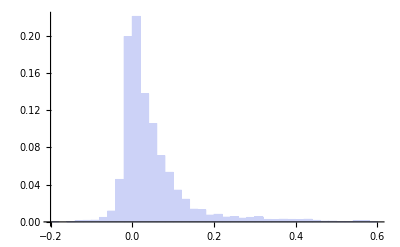

```mathematica
Histogram[dcorMinusPearson,Automatic,"Probability"]
```

```mathematica
Length[Select[dcorMinusPearson,#<=0&]]/Length[dcorMinusPearson]//N
```

0.30989

```mathematica
Length[Select[dcorMinusPearson,#==0&]]/Length[dcorMinusPearson]//N
```

0.0439322

```mathematica
Mean[dcorMinusPearson]
```

0.0463049

```mathematica
Select[Range[Length[dcorMinusPearson]],dcorMinusPearson[[#]]==0&]
```

{326,327,328,329,330,331,332,333,334,335,336,346,347,348,360,369,370,371,372,382,383,384,396,408,420,438,439,440,441,442,443,444,454,455,456,468,478,479,480,490,491,492,504,516,528,651,654,655,656,657,658,659,660,671,672,694,695,696,707,708,732,744,875,876,887,888,900,911,912,923,924,936,2597,2600,2601,2602,2603,2604,2612,2613,2614,2615,2616,2626,2627,2628,2636,2637,2638,2639,2640,2648,2649,2650,2651,2652,2662,2663,2664,2674,2675,2676,2687,2688,2699,2700,2712,3241,3242,3243,3244,3245,3246,3247,3248,3249,3250,3251,3252,3261,3262,3263,3264,3275,3276,3286,3287,3288,3298,3299,3300,3312,3323,3324,3336,3359,3360,3372,3396,3408,4116,4152,4222,4223,4224,4234,4235,4236,4247,4248,4259,4260,4271,4272,4284,4296,4308,4542,4543,4544,4545,4546,4547,4548,4557,4558,4559,4560,4571,4572,4582,4583,4584,4594,4595,4596,4607,4608,4620,4632,4647,4649,4650,4651,4652,4653,4654,4655,4656,4665,4666,4667,4668,4679,4680,4690,4691,4692,4702,4703,4704,4716,4728,4740,4760,4761,4762,4763,4764,4774,4775,4776,4788,4797,4798,4799,4800,4810,4811,4812,4824,4836,4848}

## Dependence Method best AUC counts

This redoes the analysis I did on Saturday, counting how many times a given dependence measure was the best, this time taking ties into account and leaving out pathological distributions.

Return the name of the base file and the listing of all methods (number of bins) tied for best auc in that entry. The entries are assumed to be entries in the ranked_aucs.tsv or ranked_aucs_nonpath.tsv. The method listing is sorted.

```mathematica
bestMethodsForRankedEntry[entry_List]:=With[{names=Take[entry,-8][[Range[4] 2-1]],aucs=Take[entry,-8][[Range[4] 2]],baseFile=entry[[1]]},
With[{indices=Select[Range[4],aucs[[#]]==aucs[[4]]&]},
With[{best=Sort[names[[indices]]]},
{baseFile,best}
]]]
```

```mathematica
rankedAUCData[[327]]//InputForm
```

{"rocs/00020_exp2_x000_y000.s007", ".b001.roc.tsv", 0.999999999999936, 
 ".b002.roc.tsv", 0.999891493, ".b003.roc.tsv", 0.999999999999936, ".b004.roc.tsv", 
 0.9621310765, 0, 0.000108506999936031, 0, 0.0378689234999361, -0.000108506999936031, 
 0, -0.000108506999936031, 0.0377604165000001, 0, 0.000108506999936031, 0, 
 0.0378689234999361, -0.0378689234999361, -0.0377604165000001, -0.0378689234999361, 
 0, ".b004.roc.tsv", 0.9621310765, ".b002.roc.tsv", 0.999891493, ".b001.roc.tsv", 
 0.999999999999936, ".b003.roc.tsv", 0.999999999999936}

```mathematica
bestMethodsForRankedEntry[rankedAUCData[[327]]]
```

{rocs/00020_exp2_x000_y000.s007,{.b001.roc.tsv,.b003.roc.tsv}}

```mathematica
bestAUCs=Map[bestMethodsForRankedEntry,rankedAUCData];
```

### Tally for each dependence method how many relations have that method as the best

Here we see the tallies for when a given method produces the best AUC

```mathematica
Tally[#[[2]]&/@bestAUCs]
```

{{{.b001.roc.tsv},2615},{{.b006.roc.tsv},381},{{.b004.roc.tsv},289},{{.b008.roc.tsv},73},{{.b009.roc.tsv},100},{{.b003.roc.tsv},861},{{.b001.roc.tsv,.b003.roc.tsv},28},{{.b002.roc.tsv},360},{{.b002.roc.tsv,.b004.roc.tsv},23},{{.b001.roc.tsv,.b002.roc.tsv,.b003.roc.tsv},15},{{.b010.roc.tsv},67},{{.b060.roc.tsv},33},{{.b012.roc.tsv},58},{{.b014.roc.tsv},18},{{.b016.roc.tsv},29},{{.b025.roc.tsv},35},{{.b020.roc.tsv},33},{{.b080.roc.tsv},1},{{.b018.roc.tsv},15},{{.b030.roc.tsv},17},{{.b035.roc.tsv},6},{{.b050.roc.tsv},1},{{.b095.roc.tsv},1},{{.b040.roc.tsv},4},{{.b045.roc.tsv},3},{{.b015.roc.tsv},5},{{.b070.roc.tsv},1},{{.b002.roc.tsv,.b006.roc.tsv},4}}

Code to replace strings matching the .bxxx.roc.tsv pattern where xxx is a number not 001 002 or 003 with the string MIC.

```mathematica
replaceMICBinSpecs[s_]:=Which[
Head[s]=!=String,s,
!StringMatchQ[s,".b"~~NumberString~~".roc.tsv"],s,
StringMatchQ[s,".b"~~{"001","002","003"}~~".roc.tsv"],s,
True,"MIC"]
```

```mathematica
replaceMICBinSpecs[".b016.roc.tsv"]
```

MIC

```mathematica
replaceMICBinSpecs[".b001.roc.tsv"]
```

.b001.roc.tsv

```mathematica
replaceMICBinSpecs[".foo.roc.tsv"]
```

.foo.roc.tsv

```mathematica
replaceMICBinSpecs[1]
```

1

#### Count all MIC together

Now, replacing the mic-submethods with the string MIC, we get:

```mathematica
Tally[#[[2]]&/@Map[replaceMICBinSpecs, bestAUCs,{3}]]
```

{{{.b001.roc.tsv},2615},{{MIC},1170},{{.b003.roc.tsv},861},{{.b001.roc.tsv,.b003.roc.tsv},28},{{.b002.roc.tsv},360},{{.b002.roc.tsv,MIC},27},{{.b001.roc.tsv,.b002.roc.tsv,.b003.roc.tsv},15}}

As percentages:

```mathematica
{#[[1]],Round[100#[[2]]/Length[bestAUCs]]}&/@Tally[#[[2]]&/@Map[replaceMICBinSpecs, bestAUCs,{3}]]
```

{{{.b001.roc.tsv},52},{{MIC},23},{{.b003.roc.tsv},17},{{.b001.roc.tsv,.b003.roc.tsv},1},{{.b002.roc.tsv},7},{{.b002.roc.tsv,MIC},1},{{.b001.roc.tsv,.b002.roc.tsv,.b003.roc.tsv},0}}

#### 12 or fewer samples

Looking at only the 12 or less samples we get:

```mathematica
has12OrLessSamples[filename_String]:=StringMatchQ[filename,___~~{"s005","s006","s007","s008","s009","s010","s011","s012"}~~___]
```

```mathematica
has7OrLessSamples[filename_String]:=StringMatchQ[filename,___~~{"s005","s006","s007"}~~___]
```

```mathematica
bestAUCs[[1]]
```

{rocs/00001_parabolic_x000_y000.s005,{.b001.roc.tsv}}

```mathematica
With[{aucs=Select[bestAUCs,has12OrLessSamples[#[[1]]]&]},{#[[1]],Round[100#[[2]]/Length[aucs]]}&/@Tally[#[[2]]&/@Map[replaceMICBinSpecs, aucs,{3}]]
]
```

{{{.b001.roc.tsv},54},{{MIC},16},{{.b003.roc.tsv},21},{{.b001.roc.tsv,.b003.roc.tsv},0},{{.b002.roc.tsv},8}}

#### 7 or fewer samples

And at 7 or less, we get:

```mathematica
With[{aucs=Select[bestAUCs,has7OrLessSamples[#[[1]]]&]},{#[[1]],Round[100#[[2]]/Length[aucs]]}&/@Tally[#[[2]]&/@Map[replaceMICBinSpecs, aucs,{3}]]
]
```

{{{.b001.roc.tsv},52},{{MIC},14},{{.b003.roc.tsv},25},{{.b001.roc.tsv,.b003.roc.tsv},1},{{.b002.roc.tsv},8}}

```mathematica
rankedAUCData[[1]]
```

{rocs/00001_parabolic_x000_y000.s005,.b001.roc.tsv,0.732437,.b002.roc.tsv,0.551128,.b003.roc.tsv,0.622146,.b004.roc.tsv,0.634223,0,0.181309,0.110291,0.0982138,-0.181309,0,-0.0710174,-0.0830949,-0.110291,0.0710174,0,-0.0120775,-0.0982138,0.0830949,0.0120775,0,.b002.roc.tsv,0.551128,.b003.roc.tsv,0.622146,.b004.roc.tsv,0.634223,.b001.roc.tsv,0.732437}

```mathematica
Length[rankedAUCData[[1]]]
```

33

```mathematica
bestMICTinySample=Sort[With[{aucs=Select[Map[replaceMICBinSpecs,rankedAUCData,{2}],has7OrLessSamples[#[[1]]]&]},Select[aucs,"MIC"==#[[32]]&]
],#1[[33]]<#2[[33]]&
]//Map[{#[[1]],#[[33]],#[[13]]}&,#]&;
```

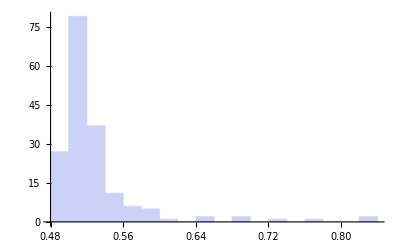

```mathematica
Histogram[#[[2]]&/@bestMICTinySample]
```

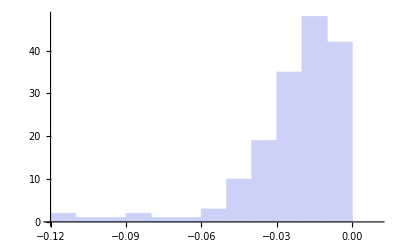

```mathematica
Histogram[#[[3]]&/@Select[bestMICTinySample,#[[2]]<0.6&]]
```

### What are the characteristics of non-random inputs which have a particular method as their best AUC detector

#### By Relation Name

When looked at by relation name, distance correlation is most frequently the best AUC dependence measure for all relations except a handful:

Pearson is better on two of the exponentials (the third is highly curved, so dCor and spearman are best for the majority), for the 1/4 sin, for categorical02 (which is the endpoints of a line), 1 line, the sigmoid and the lower frequency slanted sine waves.

Mic is only really better on the circle and sin03pi. It is also slightly better than dcor on sin13pi and varfr5c, but not by much (49 to 45 and 49 to 43 respectively).

Spearman is best on the non-coexistence relationship.

{{1,{parabolic,cubic1,cubic2,exp1e10,sin01pi,sin02pi,sin04pi,cos07pi,sin08pi,sin09pi,sin10pi,cos14pi,sin16pi,sin32pi,varfr6s,varfr7s,2sin2_3,2sin4_10,categorical05,categorical11,categorical23,categorical47,categorical95,lines3,lines4,lines5,x,lineparab,spike,L,L_lop,slsin2833033,slsin3137037}},{3,{exp2,exp10,sinhalfpi,categorical02,lines1,sigmoid,slsin0811116,slsin2105110,slsin2110106}},{-1,{sin03pi,sin13pi,varfr5c,circle}},{2,{lines2}}}

```mathematica
bestAUCs[[1]]
```

{rocs/00001_parabolic_x000_y000.s005,{.b001.roc.tsv}}

```mathematica
bestAUCEntryWithCharacteristics[entry_List]:=With[{filenames=Map[entry[[1]]~~#&,entry[[2]]]},
With[{f=filenames[[1]]},
{functionName[f],xNoise[f],yNoise[f],nSamples[f],Map[nBins, filenames]}
]]
```

```mathematica
bestAUCEntryWithCharacteristics[bestAUCs[[1]]]
```

{parabolic,0,0,5,{1}}

```mathematica
bestAUCChars=bestAUCEntryWithCharacteristics/@bestAUCs;
```

```mathematica
bestAUCCharsUnifiedMIC=Map[{#[[1]],#[[2]],#[[3]],#[[4]],Map[If[#≥4,-1,#]&,#[[5]]]}&,bestAUCChars];
```

```mathematica
Take[bestAUCCharsUnifiedMIC,20]
```

{{parabolic,0,0,5,{1}},{parabolic,0,0,6,{1}},{parabolic,0,0,7,{-1}},{parabolic,0,0,8,{-1}},{parabolic,0,0,9,{-1}},{parabolic,0,0,10,{-1}},{parabolic,0,0,12,{-1}},{parabolic,0,0,14,{-1}},{parabolic,0,0,19,{-1}},{parabolic,0,0,30,{-1}},{parabolic,0,0,60,{-1}},{parabolic,0,0,100,{-1}},{parabolic,0,1/10,5,{1}},{parabolic,0,1/10,6,{1}},{parabolic,0,1/10,7,{1}},{parabolic,0,1/10,8,{1}},{parabolic,0,1/10,9,{1}},{parabolic,0,1/10,10,{-1}},{parabolic,0,1/10,12,{-1}},{parabolic,0,1/10,14,{-1}}}

```mathematica
OrderedQ[{"parabolic","cubic1"}]
```

False

```mathematica
!True
```

False

```mathematica
Sort[Tally[Map[Join[{#[[1]]},#[[5]]]&,bestAUCCharsUnifiedMIC]],(OrderedQ[{#1[[1,1]],#2[[1,1]]}]&&!OrderedQ[{#2[[1,1]],#1[[1,1]]}])||(#1[[1,1]]==#2[[1,1]]&&#1[[2]]>#2[[2]])&]
```

{{{2sin2_3,1},90},{{2sin2_3,-1},15},{{2sin2_3,2},2},{{2sin2_3,3},1},{{2sin4_10,1},48},{{2sin4_10,3},27},{{2sin4_10,-1},23},{{2sin4_10,2},10},{{categorical02,3},45},{{categorical02,1},27},{{categorical02,-1},18},{{categorical02,1,3},8},{{categorical02,2},7},{{categorical02,2,-1},3},{{categorical05,1},66},{{categorical05,3},21},{{categorical05,-1},19},{{categorical05,2},2},{{categorical11,1},47},{{categorical11,-1},38},{{categorical11,2},15},{{categorical11,3},8},{{categorical23,1},54},{{categorical23,-1},36},{{categorical23,2},10},{{categorical23,3},8},{{categorical47,1},57},{{categorical47,-1},48},{{categorical47,3},2},{{categorical47,2},1},{{categorical95,1},60},{{categorical95,-1},48},{{circle,-1},87},{{circle,1},21},{{cos07pi,1},47},{{cos07pi,-1},47},{{cos07pi,3},8},{{cos07pi,2},6},{{cos14pi,1},44},{{cos14pi,-1},39},{{cos14pi,3},18},{{cos14pi,2},7},{{cubic1,1},95},{{cubic1,-1},13},{{cubic2,1},86},{{cubic2,-1},20},{{cubic2,3},2},{{exp10,3},59},{{exp10,1},26},{{exp10,-1},9},{{exp10,2},7},{{exp10,1,2,3},3},{{exp10,1,3},2},{{exp10,2,-1},2},{{exp1e10,1},72},{{exp1e10,2},30},{{exp1e10,-1},4},{{exp1e10,2,-1},2},{{exp2,3},64},{{exp2,1},18},{{exp2,-1},9},{{exp2,2},8},{{exp2,1,3},4},{{exp2,1,2,3},3},{{exp2,2,-1},2},{{L,1},72},{{L,2},18},{{L,3},10},{{L,-1},5},{{L,2,-1},3},{{lineparab,1},105},{{lineparab,-1},2},{{lineparab,3},1},{{lines1,3},66},{{lines1,1},12},{{lines1,2},11},{{lines1,-1},10},{{lines1,1,3},5},{{lines1,1,2,3},2},{{lines1,2,-1},2},{{lines2,2},53},{{lines2,1},31},{{lines2,3},16},{{lines2,-1},7},{{lines2,2,-1},1},{{lines3,1},63},{{lines3,-1},24},{{lines3,3},20},{{lines3,2},1},{{lines4,1},65},{{lines4,-1},29},{{lines4,2},12},{{lines4,3},2},{{lines5,1},76},{{lines5,3},17},{{lines5,-1},15},{{L_lop,1},71},{{L_lop,2},19},{{L_lop,3},11},{{L_lop,-1},5},{{L_lop,2,-1},2},{{parabolic,1},80},{{parabolic,-1},28},{{sigmoid,3},48},{{sigmoid,1},42},{{sigmoid,-1},12},{{sigmoid,2},2},{{sigmoid,1,3},2},{{sigmoid,1,2,3},1},{{sigmoid,2,-1},1},{{sin01pi,1},84},{{sin01pi,-1},24},{{sin02pi,1},88},{{sin02pi,-1},11},{{sin02pi,3},8},{{sin02pi,1,2,3},1},{{sin03pi,-1},64},{{sin03pi,1},43},{{sin03pi,2},1},{{sin04pi,1},65},{{sin04pi,-1},24},{{sin04pi,3},19},{{sin08pi,1},49},{{sin08pi,-1},30},{{sin08pi,3},21},{{sin08pi,2},8},{{sin09pi,1},49},{{sin09pi,-1},49},{{sin09pi,2},5},{{sin09pi,3},5},{{sin10pi,1},45},{{sin10pi,-1},30},{{sin10pi,3},25},{{sin10pi,2},8},{{sin13pi,-1},49},{{sin13pi,1},45},{{sin13pi,2},8},{{sin13pi,3},6},{{sin16pi,1},44},{{sin16pi,-1},39},{{sin16pi,2},14},{{sin16pi,3},11},{{sin32pi,1},47},{{sin32pi,-1},44},{{sin32pi,2},10},{{sin32pi,3},7},{{sinhalfpi,3},45},{{sinhalfpi,1},45},{{sinhalfpi,-1},8},{{sinhalfpi,2},6},{{sinhalfpi,2,-1},2},{{sinhalfpi,1,2,3},1},{{sinhalfpi,1,3},1},{{slsin0811116,3},60},{{slsin0811116,1},22},{{slsin0811116,-1},11},{{slsin0811116,2},10},{{slsin0811116,2,-1},3},{{slsin0811116,1,2,3},1},{{slsin0811116,1,3},1},{{slsin2105110,3},70},{{slsin2105110,1},13},{{slsin2105110,-1},11},{{slsin2105110,2},9},{{slsin2105110,2,-1},2},{{slsin2105110,1,3},2},{{slsin2105110,1,2,3},1},{{slsin2110106,3},69},{{slsin2110106,1},18},{{slsin2110106,-1},10},{{slsin2110106,2},5},{{slsin2110106,1,3},3},{{slsin2110106,1,2,3},2},{{slsin2110106,2,-1},1},{{slsin2833033,1},90},{{slsin2833033,-1},9},{{slsin2833033,3},8},{{slsin2833033,2},1},{{slsin3137037,1},96},{{slsin3137037,-1},12},{{spike,1},58},{{spike,2},28},{{spike,3},17},{{spike,-1},4},{{spike,2,-1},1},{{varfr5c,-1},49},{{varfr5c,1},43},{{varfr5c,2},10},{{varfr5c,3},6},{{varfr6s,1},48},{{varfr6s,-1},33},{{varfr6s,3},20},{{varfr6s,2},7},{{varfr7s,1},49},{{varfr7s,-1},40},{{varfr7s,3},10},{{varfr7s,2},9},{{x,1},99},{{x,-1},9}}

```mathematica
Sort[Tally[Map[Join[{#[[1]]},#[[5]]]&,bestAUCCharsUnifiedMIC]],(OrderedQ[{#1[[1,1]],#2[[1,1]]}]&&!OrderedQ[{#2[[1,1]],#1[[1,1]]}])||(#1[[1,1]]==#2[[1,1]]&&#1[[2]]>#2[[2]])&]
```

```mathematica
bestAUCCharsUnifiedMICNameGathered=Gather[bestAUCCharsUnifiedMIC,#1[[1]]==#2[[1]]&];
```

```mathematica
bestAUCCharsUnifiedMICNameGathered[[1]]
```

{{parabolic,0,0,5,{1}},{parabolic,0,0,6,{1}},{parabolic,0,0,7,{-1}},{parabolic,0,0,8,{-1}},{parabolic,0,0,9,{-1}},{parabolic,0,0,10,{-1}},{parabolic,0,0,12,{-1}},{parabolic,0,0,14,{-1}},{parabolic,0,0,19,{-1}},{parabolic,0,0,30,{-1}},{parabolic,0,0,60,{-1}},{parabolic,0,0,100,{-1}},{parabolic,0,1/10,5,{1}},{parabolic,0,1/10,6,{1}},{parabolic,0,1/10,7,{1}},{parabolic,0,1/10,8,{1}},{parabolic,0,1/10,9,{1}},{parabolic,0,1/10,10,{-1}},{parabolic,0,1/10,12,{-1}},{parabolic,0,1/10,14,{-1}},{parabolic,0,1/10,19,{-1}},{parabolic,0,1/10,30,{-1}},{parabolic,0,1/10,60,{-1}},{parabolic,0,1/10,100,{-1}},{parabolic,0,3/10,5,{1}},{parabolic,0,3/10,6,{1}},{parabolic,0,3/10,7,{1}},{parabolic,0,3/10,8,{1}},{parabolic,0,3/10,9,{1}},{parabolic,0,3/10,10,{1}},{parabolic,0,3/10,12,{1}},{parabolic,0,3/10,14,{1}},{parabolic,0,3/10,19,{1}},{parabolic,0,3/10,30,{1}},{parabolic,0,3/10,60,{-1}},{parabolic,0,3/10,100,{-1}},{parabolic,1/10,0,5,{1}},{parabolic,1/10,0,6,{1}},{parabolic,1/10,0,7,{1}},{parabolic,1/10,0,8,{1}},{parabolic,1/10,0,9,{1}},{parabolic,1/10,0,10,{1}},{parabolic,1/10,0,12,{1}},{parabolic,1/10,0,14,{-1}},{parabolic,1/10,0,19,{-1}},{parabolic,1/10,0,30,{-1}},{parabolic,1/10,0,60,{-1}},{parabolic,1/10,0,100,{-1}},{parabolic,1/10,1/10,5,{1}},{parabolic,1/10,1/10,6,{1}},{parabolic,1/10,1/10,7,{1}},{parabolic,1/10,1/10,8,{1}},{parabolic,1/10,1/10,9,{1}},{parabolic,1/10,1/10,10,{1}},{parabolic,1/10,1/10,12,{1}},{parabolic,1/10,1/10,14,{1}},{parabolic,1/10,1/10,19,{1}},{parabolic,1/10,1/10,30,{-1}},{parabolic,1/10,1/10,60,{-1}},{parabolic,1/10,1/10,100,{-1}},{parabolic,1/10,3/10,5,{1}},{parabolic,1/10,3/10,6,{1}},{parabolic,1/10,3/10,7,{1}},{parabolic,1/10,3/10,8,{1}},{parabolic,1/10,3/10,9,{1}},{parabolic,1/10,3/10,10,{1}},{parabolic,1/10,3/10,12,{1}},{parabolic,1/10,3/10,14,{1}},{parabolic,1/10,3/10,19,{1}},{parabolic,1/10,3/10,30,{1}},{parabolic,1/10,3/10,60,{1}},{parabolic,1/10,3/10,100,{-1}},{parabolic,3/10,0,5,{1}},{parabolic,3/10,0,6,{1}},{parabolic,3/10,0,7,{1}},{parabolic,3/10,0,8,{1}},{parabolic,3/10,0,9,{1}},{parabolic,3/10,0,10,{1}},{parabolic,3/10,0,12,{1}},{parabolic,3/10,0,14,{1}},{parabolic,3/10,0,19,{1}},{parabolic,3/10,0,30,{1}},{parabolic,3/10,0,60,{1}},{parabolic,3/10,0,100,{1}},{parabolic,3/10,1/10,5,{1}},{parabolic,3/10,1/10,6,{1}},{parabolic,3/10,1/10,7,{1}},{parabolic,3/10,1/10,8,{1}},{parabolic,3/10,1/10,9,{1}},{parabolic,3/10,1/10,10,{1}},{parabolic,3/10,1/10,12,{1}},{parabolic,3/10,1/10,14,{1}},{parabolic,3/10,1/10,19,{1}},{parabolic,3/10,1/10,30,{1}},{parabolic,3/10,1/10,60,{1}},{parabolic,3/10,1/10,100,{1}},{parabolic,3/10,3/10,5,{1}},{parabolic,3/10,3/10,6,{1}},{parabolic,3/10,3/10,7,{1}},{parabolic,3/10,3/10,8,{1}},{parabolic,3/10,3/10,9,{1}},{parabolic,3/10,3/10,10,{1}},{parabolic,3/10,3/10,12,{1}},{parabolic,3/10,3/10,14,{1}},{parabolic,3/10,3/10,19,{1}},{parabolic,3/10,3/10,30,{1}},{parabolic,3/10,3/10,60,{1}},{parabolic,3/10,3/10,100,{1}}}

```mathematica
Map[{#[[1,1]],Sort[Tally[#[[5]]&/@#],#1[[2]]>#2[[2]]&]}&,bestAUCCharsUnifiedMICNameGathered]
```

{{parabolic,{{{1},80},{{-1},28}}},{cubic1,{{{1},95},{{-1},13}}},{cubic2,{{{1},86},{{-1},20},{{3},2}}},{exp2,{{{3},64},{{1},18},{{-1},9},{{2},8},{{1,3},4},{{1,2,3},3},{{2,-1},2}}},{exp10,{{{3},59},{{1},26},{{-1},9},{{2},7},{{1,2,3},3},{{1,3},2},{{2,-1},2}}},{exp1e10,{{{1},72},{{2},30},{{-1},4},{{2,-1},2}}},{sinhalfpi,{{{3},45},{{1},45},{{-1},8},{{2},6},{{2,-1},2},{{1,2,3},1},{{1,3},1}}},{sin01pi,{{{1},84},{{-1},24}}},{sin02pi,{{{1},88},{{-1},11},{{3},8},{{1,2,3},1}}},{sin03pi,{{{-1},64},{{1},43},{{2},1}}},{sin04pi,{{{1},65},{{-1},24},{{3},19}}},{cos07pi,{{{1},47},{{-1},47},{{3},8},{{2},6}}},{sin08pi,{{{1},49},{{-1},30},{{3},21},{{2},8}}},{sin09pi,{{{1},49},{{-1},49},{{2},5},{{3},5}}},{sin10pi,{{{1},45},{{-1},30},{{3},25},{{2},8}}},{sin13pi,{{{-1},49},{{1},45},{{2},8},{{3},6}}},{cos14pi,{{{1},44},{{-1},39},{{3},18},{{2},7}}},{sin16pi,{{{1},44},{{-1},39},{{2},14},{{3},11}}},{sin32pi,{{{1},47},{{-1},44},{{2},10},{{3},7}}},{varfr5c,{{{-1},49},{{1},43},{{2},10},{{3},6}}},{varfr6s,{{{1},48},{{-1},33},{{3},20},{{2},7}}},{varfr7s,{{{1},49},{{-1},40},{{3},10},{{2},9}}},{2sin2_3,{{{1},90},{{-1},15},{{2},2},{{3},1}}},{2sin4_10,{{{1},48},{{3},27},{{-1},23},{{2},10}}},{categorical02,{{{3},45},{{1},27},{{-1},18},{{1,3},8},{{2},7},{{2,-1},3}}},{categorical05,{{{1},66},{{3},21},{{-1},19},{{2},2}}},{categorical11,{{{1},47},{{-1},38},{{2},15},{{3},8}}},{categorical23,{{{1},54},{{-1},36},{{2},10},{{3},8}}},{categorical47,{{{1},57},{{-1},48},{{3},2},{{2},1}}},{categorical95,{{{1},60},{{-1},48}}},{lines1,{{{3},66},{{1},12},{{2},11},{{-1},10},{{1,3},5},{{1,2,3},2},{{2,-1},2}}},{lines2,{{{2},53},{{1},31},{{3},16},{{-1},7},{{2,-1},1}}},{lines3,{{{1},63},{{-1},24},{{3},20},{{2},1}}},{lines4,{{{1},65},{{-1},29},{{2},12},{{3},2}}},{lines5,{{{1},76},{{3},17},{{-1},15}}},{x,{{{1},99},{{-1},9}}},{circle,{{{-1},87},{{1},21}}},{lineparab,{{{1},105},{{-1},2},{{3},1}}},{spike,{{{1},58},{{2},28},{{3},17},{{-1},4},{{2,-1},1}}},{sigmoid,{{{3},48},{{1},42},{{-1},12},{{2},2},{{1,3},2},{{1,2,3},1},{{2,-1},1}}},{L,{{{1},72},{{2},18},{{3},10},{{-1},5},{{2,-1},3}}},{L_lop,{{{1},71},{{2},19},{{3},11},{{-1},5},{{2,-1},2}}},{slsin0811116,{{{3},60},{{1},22},{{-1},11},{{2},10},{{2,-1},3},{{1,2,3},1},{{1,3},1}}},{slsin2105110,{{{3},70},{{1},13},{{-1},11},{{2},9},{{2,-1},2},{{1,3},2},{{1,2,3},1}}},{slsin2110106,{{{3},69},{{1},18},{{-1},10},{{2},5},{{1,3},3},{{1,2,3},2},{{2,-1},1}}},{slsin2833033,{{{1},90},{{-1},9},{{3},8},{{2},1}}},{slsin3137037,{{{1},96},{{-1},12}}}}

```mathematica
Column[%]
```

{parabolic,{{{1},80},{{-1},28}}}
{cubic1,{{{1},95},{{-1},13}}}
{cubic2,{{{1},86},{{-1},20},{{3},2}}}
{exp2,{{{3},64},{{1},18},{{-1},9},{{2},8},{{1,3},4},{{1,2,3},3},{{2,-1},2}}}
{exp10,{{{3},59},{{1},26},{{-1},9},{{2},7},{{1,2,3},3},{{1,3},2},{{2,-1},2}}}
{exp1e10,{{{1},72},{{2},30},{{-1},4},{{2,-1},2}}}
{sinhalfpi,{{{3},45},{{1},45},{{-1},8},{{2},6},{{2,-1},2},{{1,2,3},1},{{1,3},1}}}
{sin01pi,{{{1},84},{{-1},24}}}
{sin02pi,{{{1},88},{{-1},11},{{3},8},{{1,2,3},1}}}
{sin03pi,{{{-1},64},{{1},43},{{2},1}}}
{sin04pi,{{{1},65},{{-1},24},{{3},19}}}
{cos07pi,{{{1},47},{{-1},47},{{3},8},{{2},6}}}
{sin08pi,{{{1},49},{{-1},30},{{3},21},{{2},8}}}
{sin09pi,{{{1},49},{{-1},49},{{2},5},{{3},5}}}
{sin10pi,{{{1},45},{{-1},30},{{3},25},{{2},8}}}
{sin13pi,{{{-1},49},{{1},45},{{2},8},{{3},6}}}
{cos14pi,{{{1},44},{{-1},39},{{3},18},{{2},7}}}
{sin16pi,{{{1},44},{{-1},39},{{2},14},{{3},11}}}
{sin32pi,{{{1},47},{{-1},44},{{2},10},{{3},7}}}
{varfr5c,{{{-1},49},{{1},43},{{2},10},{{3},6}}}
{varfr6s,{{{1},48},{{-1},33},{{3},20},{{2},7}}}
{varfr7s,{{{1},49},{{-1},40},{{3},10},{{2},9}}}
{2sin2_3,{{{1},90},{{-1},15},{{2},2},{{3},1}}}
{2sin4_10,{{{1},48},{{3},27},{{-1},23},{{2},10}}}
{categorical02,{{{3},45},{{1},27},{{-1},18},{{1,3},8},{{2},7},{{2,-1},3}}}
{categorical05,{{{1},66},{{3},21},{{-1},19},{{2},2}}}
{categorical11,{{{1},47},{{-1},38},{{2},15},{{3},8}}}
{categorical23,{{{1},54},{{-1},36},{{2},10},{{3},8}}}
{categorical47,{{{1},57},{{-1},48},{{3},2},{{2},1}}}
{categorical95,{{{1},60},{{-1},48}}}
{lines1,{{{3},66},{{1},12},{{2},11},{{-1},10},{{1,3},5},{{1,2,3},2},{{2,-1},2}}}
{lines2,{{{2},53},{{1},31},{{3},16},{{-1},7},{{2,-1},1}}}
{lines3,{{{1},63},{{-1},24},{{3},20},{{2},1}}}
{lines4,{{{1},65},{{-1},29},{{2},12},{{3},2}}}
{lines5,{{{1},76},{{3},17},{{-1},15}}}
{x,{{{1},99},{{-1},9}}}
{circle,{{{-1},87},{{1},21}}}
{lineparab,{{{1},105},{{-1},2},{{3},1}}}
{spike,{{{1},58},{{2},28},{{3},17},{{-1},4},{{2,-1},1}}}
{sigmoid,{{{3},48},{{1},42},{{-1},12},{{2},2},{{1,3},2},{{1,2,3},1},{{2,-1},1}}}
{L,{{{1},72},{{2},18},{{3},10},{{-1},5},{{2,-1},3}}}
{L_lop,{{{1},71},{{2},19},{{3},11},{{-1},5},{{2,-1},2}}}
{slsin0811116,{{{3},60},{{1},22},{{-1},11},{{2},10},{{2,-1},3},{{1,2,3},1},{{1,3},1}}}
{slsin2105110,{{{3},70},{{1},13},{{-1},11},{{2},9},{{2,-1},2},{{1,3},2},{{1,2,3},1}}}
{slsin2110106,{{{3},69},{{1},18},{{-1},10},{{2},5},{{1,3},3},{{1,2,3},2},{{2,-1},1}}}
{slsin2833033,{{{1},90},{{-1},9},{{3},8},{{2},1}}}
{slsin3137037,{{{1},96},{{-1},12}}}

```mathematica
Map[{#[[1,2]],Map[#[[1]]&,#]}&,Gather[Map[{#[[1]],First[#[[2,1,1]]]}&,Map[{#[[1,1]],Sort[Tally[#[[5]]&/@#],#1[[2]]>#2[[2]]&]}&,bestAUCCharsUnifiedMICNameGathered]],#1[[2]]==#2[[2]]&]]
```

{{1,{parabolic,cubic1,cubic2,exp1e10,sin01pi,sin02pi,sin04pi,cos07pi,sin08pi,sin09pi,sin10pi,cos14pi,sin16pi,sin32pi,varfr6s,varfr7s,2sin2_3,2sin4_10,categorical05,categorical11,categorical23,categorical47,categorical95,lines3,lines4,lines5,x,lineparab,spike,L,L_lop,slsin2833033,slsin3137037}},{3,{exp2,exp10,sinhalfpi,categorical02,lines1,sigmoid,slsin0811116,slsin2105110,slsin2110106}},{-1,{sin03pi,sin13pi,varfr5c,circle}},{2,{lines2}}}

#### Only look at clear relationships

Some inputs are not easy to distinguish from being random. I already removed the pathological relations from the mix. Let's see what the tallies are when we remove all difficult inputs, that is, remove all the inputs that have an AUC less than 0.90 for the best method.

```mathematica
rankedAUCDataEasy=Select[rankedAUCData,#[[33]]≥0.90&];(*slot 33 is the auc for the best method*)
```

```mathematica
Length[rankedAUCData]
```

5076

```mathematica
Length[rankedAUCDataEasy]
```

1397

```mathematica
bestAUCsEasy=bestMethodsForRankedEntry/@rankedAUCDataEasy;
```

##### Count

Now, replacing the mic-submethods with the string MIC, we get:

```mathematica
Sort[Tally[#[[2]]&/@Map[replaceMICBinSpecs, bestAUCsEasy,{3}]],#1[[2]]>#2[[2]]&]
```

{{{.b003.roc.tsv},441},{{MIC},431},{{.b001.roc.tsv},277},{{.b002.roc.tsv},178},{{.b001.roc.tsv,.b003.roc.tsv},28},{{.b002.roc.tsv,MIC},27},{{.b001.roc.tsv,.b002.roc.tsv,.b003.roc.tsv},15}}

```mathematica
{#[[1]],Round[100#[[2]]/Length[bestAUCsEasy]]}&/@Sort[Tally[#[[2]]&/@Map[replaceMICBinSpecs, bestAUCsEasy,{3}]],#1[[2]]>#2[[2]]&]
```

{{{.b003.roc.tsv},32},{{MIC},31},{{.b001.roc.tsv},20},{{.b002.roc.tsv},13},{{.b001.roc.tsv,.b003.roc.tsv},2},{{.b002.roc.tsv,MIC},2},{{.b001.roc.tsv,.b002.roc.tsv,.b003.roc.tsv},1}}

Not replacing the mic bin counts, we get

```mathematica
Sort[Tally[#[[2]]&/@bestAUCsEasy],#1[[2]]>#2[[2]]&]
```

{{{.b003.roc.tsv},441},{{.b001.roc.tsv},277},{{.b002.roc.tsv},178},{{.b004.roc.tsv},134},{{.b006.roc.tsv},99},{{.b060.roc.tsv},33},{{.b009.roc.tsv},29},{{.b001.roc.tsv,.b003.roc.tsv},28},{{.b008.roc.tsv},27},{{.b002.roc.tsv,.b004.roc.tsv},23},{{.b020.roc.tsv},22},{{.b025.roc.tsv},22},{{.b030.roc.tsv},15},{{.b001.roc.tsv,.b002.roc.tsv,.b003.roc.tsv},15},{{.b010.roc.tsv},14},{{.b016.roc.tsv},11},{{.b012.roc.tsv},7},{{.b018.roc.tsv},7},{{.b035.roc.tsv},5},{{.b002.roc.tsv,.b006.roc.tsv},4},{{.b040.roc.tsv},4},{{.b014.roc.tsv},1},{{.b070.roc.tsv},1}}

As percentages:

```mathematica
{#[[1]],Round[100#[[2]]/Length[bestAUCsEasy]]}&/@Sort[Tally[#[[2]]&/@bestAUCsEasy],#1[[2]]>#2[[2]]&]
```

{{{.b003.roc.tsv},32},{{.b001.roc.tsv},20},{{.b002.roc.tsv},13},{{.b004.roc.tsv},10},{{.b006.roc.tsv},7},{{.b060.roc.tsv},2},{{.b009.roc.tsv},2},{{.b001.roc.tsv,.b003.roc.tsv},2},{{.b008.roc.tsv},2},{{.b002.roc.tsv,.b004.roc.tsv},2},{{.b020.roc.tsv},2},{{.b025.roc.tsv},2},{{.b030.roc.tsv},1},{{.b001.roc.tsv,.b002.roc.tsv,.b003.roc.tsv},1},{{.b010.roc.tsv},1},{{.b016.roc.tsv},1},{{.b012.roc.tsv},1},{{.b018.roc.tsv},1},{{.b035.roc.tsv},0},{{.b002.roc.tsv,.b006.roc.tsv},0},{{.b040.roc.tsv},0},{{.b014.roc.tsv},0},{{.b070.roc.tsv},0}}

Now, further broken down by sample size

```mathematica
bestAUCCharsEasy=bestAUCEntryWithCharacteristics/@bestAUCsEasy;
```

```mathematica
Sort[GatherBy[Sort[Tally[#[[{4,5}]]&/@bestAUCCharsEasy],#1[[2]]>#2[[2]]&],#[[1,1]]&],#1[[1,1,1]]>#2[[1,1,1]]&]
```

{{{{100,{4}},82},{{100,{1}},51},{{100,{60}},33},{{100,{6}},30},{{100,{1,2,3}},15},{{100,{9}},15},{{100,{3}},12},{{100,{20}},7},{{100,{30}},6},{{100,{2}},6},{{100,{25}},3},{{100,{16}},3},{{100,{12}},2},{{100,{40}},2},{{100,{8}},2},{{100,{10}},2},{{100,{1,3}},1},{{100,{35}},1},{{100,{14}},1},{{100,{70}},1}},{{{60,{4}},52},{{60,{1}},44},{{60,{6}},34},{{60,{3}},22},{{60,{25}},19},{{60,{2}},19},{{60,{30}},9},{{60,{20}},8},{{60,{9}},8},{{60,{8}},6},{{60,{35}},4},{{60,{10}},4},{{60,{16}},3},{{60,{12}},2},{{60,{40}},2},{{60,{18}},1}},{{{30,{1}},41},{{30,{3}},34},{{30,{2}},29},{{30,{2,4}},15},{{30,{6}},14},{{30,{20}},7},{{30,{18}},6},{{30,{8}},6},{{30,{16}},5},{{30,{10}},5},{{30,{1,3}},5},{{30,{2,6}},4},{{30,{9}},3},{{30,{12}},2}},{{{19,{3}},41},{{19,{1}},37},{{19,{2}},16},{{19,{1,3}},9},{{19,{2,4}},8},{{19,{6}},7},{{19,{8}},6},{{19,{10}},3},{{19,{12}},1},{{19,{9}},1}},{{{14,{3}},51},{{14,{2}},22},{{14,{1}},18},{{14,{8}},5},{{14,{6}},5},{{14,{1,3}},4},{{14,{9}},2}},{{{12,{3}},48},{{12,{1}},22},{{12,{2}},22},{{12,{6}},3},{{12,{8}},2}},{{{10,{3}},49},{{10,{2}},19},{{10,{1}},13},{{10,{6}},2}},{{{9,{3}},44},{{9,{2}},17},{{9,{1}},12},{{9,{6}},2}},{{{8,{3}},33},{{8,{1}},14},{{8,{2}},10},{{8,{1,3}},2},{{8,{6}},2}},{{{7,{3}},36},{{7,{1}},10},{{7,{2}},7},{{7,{1,3}},4}},{{{6,{3}},34},{{6,{1}},10},{{6,{2}},7},{{6,{1,3}},2}},{{{5,{3}},37},{{5,{1}},5},{{5,{2}},4},{{5,{1,3}},1}}}

```mathematica
bestAUCCharsEasyNameSampGathered={{#[[1,1]],#[[1,2]]},#[[3]]&/@#}&/@GatherBy[{#[[1]],#[[4]],#[[5]]}&/@bestAUCCharsEasy,{#[[1]],#[[2]]}&];
```

```mathematica
foo=GatherBy[{#[[1]],#[[4]],#[[5]]}&/@bestAUCCharsEasy,{#[[1]],#[[2]]}&];
```

```mathematica
foo[[1]]
```

{{parabolic,8,{6}}}

##### By name

```mathematica
bestAUCCharsEasy=bestAUCEntryWithCharacteristics/@bestAUCsEasy;
```

```mathematica
bestAUCCharsEasyUnifiedMIC=Map[{#[[1]],#[[2]],#[[3]],#[[4]],Map[If[#≥4,-1,#]&,#[[5]]]}&,bestAUCCharsEasy];
```

```mathematica
bestAUCCharsEasyUnifiedMICNameGathered=Gather[bestAUCCharsEasyUnifiedMIC,#1[[1]]==#2[[1]]&];
```

```mathematica
Column[Map[{#[[1,1]],Sort[Tally[#[[5]]&/@#],#1[[2]]>#2[[2]]&]}&,bestAUCCharsEasyUnifiedMICNameGathered]]
```

{parabolic,{{{-1},25},{{1},5}}}
{cubic1,{{{-1},13},{{1},8}}}
{cubic2,{{{-1},17},{{1},12}}}
{exp2,{{{3},49},{{-1},9},{{2},8},{{1},6},{{1,3},4},{{1,2,3},3},{{2,-1},2}}}
{exp10,{{{3},41},{{1},12},{{-1},9},{{2},7},{{1,2,3},3},{{1,3},2},{{2,-1},2}}}
{exp1e10,{{{2},25},{{1},7},{{-1},4},{{2,-1},2}}}
{sinhalfpi,{{{3},36},{{1},12},{{-1},8},{{2},6},{{2,-1},2},{{1,2,3},1},{{1,3},1}}}
{sin01pi,{{{-1},19},{{1},5}}}
{sin02pi,{{{1},56},{{-1},11},{{3},2},{{1,2,3},1}}}
{sin03pi,{{{-1},21}}}
{sin04pi,{{{-1},16},{{1},5},{{3},2}}}
{cos07pi,{{{-1},8}}}
{sin08pi,{{{-1},8}}}
{sin09pi,{{{-1},8}}}
{sin10pi,{{{-1},8}}}
{sin13pi,{{{-1},6}}}
{cos14pi,{{{-1},6}}}
{sin16pi,{{{-1},6}}}
{sin32pi,{{{-1},3}}}
{varfr5c,{{{-1},8}}}
{varfr6s,{{{-1},7}}}
{varfr7s,{{{-1},6}}}
{2sin2_3,{{{1},12},{{-1},8}}}
{2sin4_10,{{{-1},5}}}
{categorical02,{{{3},45},{{1},25},{{-1},18},{{1,3},8},{{2},7},{{2,-1},3}}}
{categorical05,{{{1},18},{{-1},17},{{3},2}}}
{categorical11,{{{-1},12}}}
{categorical23,{{{-1},8}}}
{categorical47,{{{-1},7}}}
{categorical95,{{{-1},3}}}
{lines1,{{{3},49},{{2},11},{{-1},10},{{1,3},5},{{1},2},{{1,2,3},2},{{2,-1},2}}}
{lines2,{{{2},28},{{1},11},{{-1},7},{{3},1},{{2,-1},1}}}
{lines3,{{{-1},7},{{1},1}}}
{lines4,{{{-1},4}}}
{lines5,{{{-1},4}}}
{x,{{{-1},8}}}
{circle,{{{-1},8}}}
{lineparab,{{{1},19},{{-1},2}}}
{spike,{{{2},24},{{3},7},{{1},4},{{-1},4},{{2,-1},1}}}
{sigmoid,{{{3},35},{{1},31},{{-1},12},{{1,3},2},{{1,2,3},1},{{2},1},{{2,-1},1}}}
{L,{{{2},18},{{-1},5},{{3},4},{{2,-1},3}}}
{L_lop,{{{2},19},{{-1},5},{{3},4},{{2,-1},2}}}
{slsin0811116,{{{3},49},{{1},12},{{-1},11},{{2},10},{{2,-1},3},{{1,2,3},1},{{1,3},1}}}
{slsin2105110,{{{3},56},{{-1},11},{{2},9},{{1},4},{{2,-1},2},{{1,3},2},{{1,2,3},1}}}
{slsin2110106,{{{3},56},{{-1},10},{{1},6},{{2},5},{{1,3},3},{{1,2,3},2},{{2,-1},1}}}
{slsin2833033,{{{-1},9},{{3},3},{{1},3}}}
{slsin3137037,{{{-1},10},{{1},1}}}

```mathematica
bestAUCCharsEasyNameGathered=Gather[bestAUCCharsEasy,#1[[1]]==#2[[1]]&];
```

Here I break MIC into its individual bin components

```mathematica
Column[Map[{#[[1,1]],Sort[Tally[#[[5]]&/@#],#1[[2]]>#2[[2]]&]}&,bestAUCCharsEasyNameGathered]]
```

{parabolic,{{{6},23},{{1},5},{{4},2}}}
{cubic1,{{{1},8},{{8},8},{{9},2},{{6},2},{{4},1}}}
{cubic2,{{{1},12},{{6},6},{{8},5},{{9},4},{{4},2}}}
{exp2,{{{3},49},{{4},9},{{2},8},{{1},6},{{1,3},4},{{1,2,3},3},{{2,4},2}}}
{exp10,{{{3},41},{{1},12},{{4},9},{{2},7},{{1,2,3},3},{{1,3},2},{{2,4},2}}}
{exp1e10,{{{2},25},{{1},7},{{4},4},{{2,4},2}}}
{sinhalfpi,{{{3},36},{{1},12},{{4},6},{{2},6},{{6},2},{{2,4},2},{{1,2,3},1},{{1,3},1}}}
{sin01pi,{{{6},17},{{1},5},{{9},1},{{4},1}}}
{sin02pi,{{{1},56},{{4},9},{{3},2},{{6},2},{{1,2,3},1}}}
{sin03pi,{{{6},12},{{10},3},{{8},3},{{60},2},{{9},1}}}
{sin04pi,{{{10},6},{{8},6},{{1},5},{{3},2},{{9},1},{{60},1},{{4},1},{{6},1}}}
{cos07pi,{{{16},5},{{60},2},{{25},1}}}
{sin08pi,{{{18},2},{{60},2},{{16},2},{{20},1},{{25},1}}}
{sin09pi,{{{20},2},{{60},2},{{25},2},{{18},2}}}
{sin10pi,{{{20},4},{{60},2},{{25},2}}}
{sin13pi,{{{30},4},{{60},2}}}
{cos14pi,{{{30},3},{{60},2},{{35},1}}}
{sin16pi,{{{40},2},{{60},2},{{35},2}}}
{sin32pi,{{{60},2},{{70},1}}}
{varfr5c,{{{25},3},{{60},2},{{18},2},{{30},1}}}
{varfr6s,{{{25},3},{{60},2},{{30},1},{{20},1}}}
{varfr7s,{{{30},3},{{60},2},{{35},1}}}
{2sin2_3,{{{1},12},{{6},6},{{10},1},{{9},1}}}
{2sin4_10,{{{20},2},{{25},2},{{30},1}}}
{categorical02,{{{3},45},{{1},25},{{4},17},{{1,3},8},{{2},7},{{2,4},3},{{6},1}}}
{categorical05,{{{1},18},{{10},4},{{8},4},{{6},4},{{4},3},{{3},2},{{9},1},{{12},1}}}
{categorical11,{{{12},6},{{16},2},{{20},1},{{9},1},{{60},1},{{25},1}}}
{categorical23,{{{20},3},{{25},2},{{16},2},{{60},1}}}
{categorical47,{{{30},2},{{35},1},{{14},1},{{25},1},{{60},1},{{18},1}}}
{categorical95,{{{40},2},{{60},1}}}
{lines1,{{{3},49},{{2},11},{{4},10},{{1,3},5},{{1},2},{{1,2,3},2},{{2,4},2}}}
{lines2,{{{2},28},{{1},11},{{4},5},{{6},2},{{3},1},{{2,4},1}}}
{lines3,{{{6},7},{{1},1}}}
{lines4,{{{9},2},{{8},1},{{6},1}}}
{lines5,{{{6},4}}}
{x,{{{9},7},{{6},1}}}
{circle,{{{9},7},{{6},1}}}
{lineparab,{{{1},19},{{6},1},{{9},1}}}
{spike,{{{2},24},{{3},7},{{1},4},{{4},4},{{2,4},1}}}
{sigmoid,{{{3},35},{{1},31},{{4},11},{{1,3},2},{{1,2,3},1},{{6},1},{{2},1},{{2,4},1}}}
{L,{{{2},18},{{4},5},{{3},4},{{2,4},2},{{2,6},1}}}
{L_lop,{{{2},19},{{4},4},{{3},4},{{6},1},{{2,6},1},{{2,4},1}}}
{slsin0811116,{{{3},49},{{1},12},{{4},10},{{2},10},{{2,4},2},{{1,2,3},1},{{6},1},{{2,6},1},{{1,3},1}}}
{slsin2105110,{{{3},56},{{4},10},{{2},9},{{1},4},{{2,4},2},{{1,3},2},{{1,2,3},1},{{6},1}}}
{slsin2110106,{{{3},56},{{4},9},{{1},6},{{2},5},{{1,3},3},{{1,2,3},2},{{6},1},{{2,6},1}}}
{slsin2833033,{{{20},5},{{3},3},{{1},3},{{60},2},{{6},1},{{25},1}}}
{slsin3137037,{{{25},3},{{20},3},{{4},2},{{60},2},{{1},1}}}

##### Which versions of MIC are best for each clear name and when

```mathematica
Select[bestAUCCharsEasy,#[[1]]=="cubic2"&&MemberQ[#[[5]],x_/;x>3]&]
```

{{cubic2,0,0,12,{8}},{cubic2,0,0,14,{8}},{cubic2,0,0,19,{8}},{cubic2,0,0,30,{8}},{cubic2,0,0,60,{6}},{cubic2,0,0,100,{4}},{cubic2,0,1/10,14,{9}},{cubic2,0,1/10,19,{9}},{cubic2,0,1/10,30,{8}},{cubic2,0,1/10,60,{6}},{cubic2,0,1/10,100,{4}},{cubic2,0,3/10,60,{9}},{cubic2,0,3/10,100,{9}},{cubic2,1/10,0,60,{6}},{cubic2,1/10,0,100,{6}},{cubic2,1/10,1/10,60,{6}},{cubic2,1/10,1/10,100,{6}}}

```mathematica
Select[bestAUCCharsEasy,#[[1]]=="exp2"&&MemberQ[#[[5]],x_/;x>3]&]
```

{{exp2,0,0,19,{2,4}},{exp2,0,0,30,{2,4}},{exp2,0,0,60,{4}},{exp2,0,0,100,{4}},{exp2,0,1/10,60,{4}},{exp2,0,1/10,100,{4}},{exp2,1/10,0,60,{4}},{exp2,1/10,0,100,{4}},{exp2,1/10,1/10,60,{4}},{exp2,1/10,1/10,100,{4}},{exp2,3/10,0,100,{4}}}

```mathematica
Select[bestAUCCharsEasy,#[[1]]=="exp10"&&MemberQ[#[[5]],x_/;x>3]&]
```

{{exp10,0,0,19,{2,4}},{exp10,0,0,30,{2,4}},{exp10,0,0,60,{4}},{exp10,0,0,100,{4}},{exp10,0,1/10,60,{4}},{exp10,0,1/10,100,{4}},{exp10,1/10,0,60,{4}},{exp10,1/10,0,100,{4}},{exp10,1/10,1/10,60,{4}},{exp10,1/10,1/10,100,{4}},{exp10,3/10,0,100,{4}}}

```mathematica
Select[bestAUCCharsEasy,#[[1]]=="lines1"&&MemberQ[#[[5]],x_/;x>3]&]
```

{{lines1,0,0,19,{2,4}},{lines1,0,0,30,{2,4}},{lines1,0,0,60,{4}},{lines1,0,0,100,{4}},{lines1,0,1/10,60,{4}},{lines1,0,1/10,100,{4}},{lines1,0,3/10,100,{4}},{lines1,1/10,0,60,{4}},{lines1,1/10,0,100,{4}},{lines1,1/10,1/10,60,{4}},{lines1,1/10,1/10,100,{4}},{lines1,3/10,0,100,{4}}}

```mathematica
Select[bestAUCCharsEasy,#[[1]]=="lines2"&&MemberQ[#[[5]],x_/;x>3]&]
```

{{lines2,0,0,30,{2,4}},{lines2,0,0,60,{4}},{lines2,0,0,100,{4}},{lines2,0,1/10,60,{6}},{lines2,0,1/10,100,{4}},{lines2,1/10,0,60,{6}},{lines2,1/10,0,100,{4}},{lines2,1/10,1/10,100,{4}}}